```mathematica
V[x_,y_,z_]:=Sqrt[(x^2+y^2+z^2)]^(-1)+(10-(Sqrt[x^2+y^2+z^2]))^(-1)
```

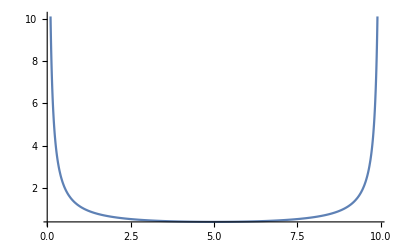

```mathematica
Plot[x^(-1)+(10-x)^(-1),{x,0.1,9.9},PlotRange->All]
```

```mathematica
gradV[x_,y_,z_]:={Evaluate[D[V[x,y,z],x]],Evaluate[D[V[x,y,z],y]],Evaluate[D[V[x,y,z],z]]}
```

```mathematica
gradV[x,y,z]
```

{-x/((x^2+y^2+z^2)^(3/2))+x/(√(x^2+y^2+z^2) (10-√(x^2+y^2+z^2))^2),-y/((x^2+y^2+z^2)^(3/2))+y/(√(x^2+y^2+z^2) (10-√(x^2+y^2+z^2))^2),-z/((x^2+y^2+z^2)^(3/2))+z/(√(x^2+y^2+z^2) (10-√(x^2+y^2+z^2))^2)}

```mathematica
D[Sqrt[x[t]^2+y[t]^2+z[t]^2],t]
```

(2 x[t] x'[t]+2 y[t] y'[t]+2 z[t] z'[t])/(2 √(x[t]^2+y[t]^2+z[t]^2))

```mathematica
SeedRandom[42]
```

```mathematica
xvec=Round[100*RandomReal[{-1,1},10]]/100;
yvec=Round[100*RandomReal[{-1,1},10]]/100;
zvec=Round[100*RandomReal[{-1,1},10]]/100;
xdotvec=Round[100*RandomReal[{-1,1},10]]/100;
ydotvec=Round[100*RandomReal[{-1,1},10]]/100;
zdotvec=Round[100*RandomReal[{-1,1},10]]/100;
```

```mathematica
For[i=1,i≤10,i+=1,
ft=20;
mysol=NDSolve[{x''[t]==-gradV[x[t],y[t],z[t]][[1]],y''[t]==-gradV[x[t],y[t],z[t]][[2]],z''[t]==-gradV[x[t],y[t],z[t]][[3]],x[0]==xvec[[i]],y[0]==yvec[[i]],z[0]==zvec[[i]],x'[0]==xdotvec[[i]],y'[0]==ydotvec[[i]],z'[0]==zdotvec[[i]]},{x,y,z},{t,0,ft},WorkingPrecision->32,Method->{"TimeIntegration"->"ExplicitRungeKutta"}];
mytab=Table[{Sqrt[x[t]^2+y[t]^2+z[t]^2],(2 x[t] x'[t]+2 y[t] y'[t]+2 z[t] z'[t])/(2 √(x[t]^2+y[t]^2+z[t]^2))} /. mysol,{t,0,ft,0.001}];
Export[StringJoin["myr",ToString[i],".csv"],mytab];
]
```

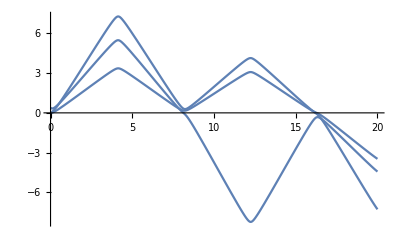

```mathematica
Plot[{x[t],y[t],z[t]} /. mysol,{t,0,ft}]
```

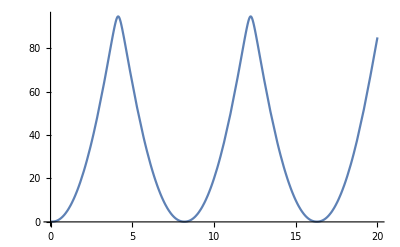

```mathematica
Plot[x[t]^2+y[t]^2+z[t]^2 /. mysol,{t,0,ft}]
```

```mathematica
i=1;
l=Norm[Cross[{xvec[[i]],yvec[[i]],zvec[[i]]},{xdotvec[[i]],ydotvec[[i]],zdotvec[[i]]}]]
```

(3 √992901)/10000

```mathematica
r0=N[Sqrt[xvec[[i]]^2 + yvec[[i]]^2 + zvec[[i]]^2]]
```

0.506458

```mathematica
rp0=N[(Evaluate[D[Sqrt[x[t]^2+y[t]^2+z[t]^2],t]] /. t->0) /. {x[0]->xvec[[i]],y[0]->yvec[[i]],z[0]->zvec[[i]],x'[0]->xdotvec[[i]],y'[0]->ydotvec[[i]],z'[0]->zdotvec[[i]]}]
```

-0.428268

```mathematica
r0=Sqrt[x[t]^2+y[t]^2+z[t]^2] /. t->0 /. mysol
```

ReplaceAll::reps: {mysol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

√(x[0]^2+y[0]^2+z[0]^2)/.mysol

```mathematica
rp0=D[Sqrt[x[t]^2+y[t]^2+z[t]^2],t] /. t->0 /. mysol
```

ReplaceAll::reps: {mysol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(2 x[0] x'[0]+2 y[0] y'[0]+2 z[0] z'[0])/(2 √(x[0]^2+y[0]^2+z[0]^2))/.mysol

```mathematica
l = Sqrt[93103091]/10000;
Veff[r_]:=r^(-1) + (10-r)^(-1)+l^2/(2 r^2)
```

```mathematica
rsol=NDSolve[{r''[t]==-Veff'[r[t]],r[0]==r0[[1]],r'[0]==rp0[[1]]},r[t],{t,0,ft},WorkingPrecision->32]
```

NDSolve::precw: The precision of the differential equation ({{r''[t]==-1/(10+Times[«2»])^2+16110497/(100000000 r[t]^3)+1/r[t]^2,r[0]==0.3837968212479097643939848432436,r'[0]==-0.96170676661645277690305367034},{},{},{},{}}) is less than WorkingPrecision (32.).

{{r[t]→InterpolatingFunction[{{0, 20.000000000000000000000000000000}}, <>][t]}}

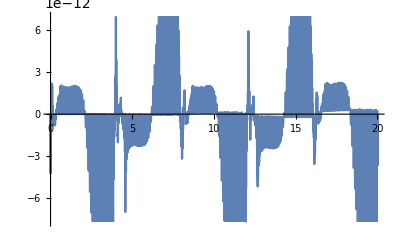

```mathematica
Plot[{Evaluate[Sqrt[x[t]^2+y[t]^2+z[t]^2] /. mysol]- Evaluate[r[t] /. rsol]},{t,0,ft}]
```

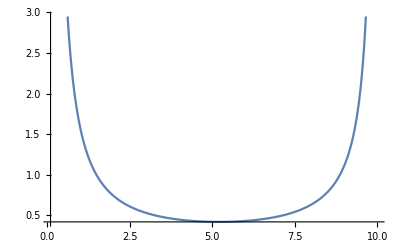

```mathematica
Plot[Veff[r],{r,0.1,9.9999}]
```

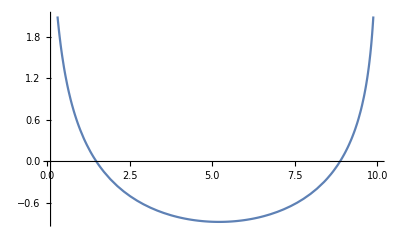

```mathematica
Plot[Log[Veff[r]],{r,0.1,9.9999}]
```

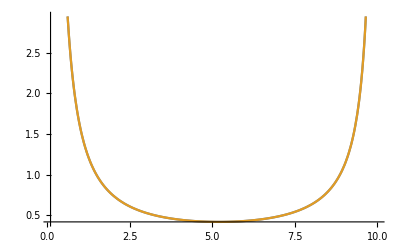

```mathematica
Plot[{Veff[r],Evaluate[PadeApproximant[Veff[r],{r,10,3}]]},{r,0.1,9.9999}]
```

```mathematica
Evaluate[PadeApproximant[Veff[r],{r,10,{1,3}}]]
```

(-1-(1906896909 (-10+r))/20000000000)/(-10+1/5 (-10+r)^2+1/100 (-10+r)^3+r)

```mathematica
FullSimplify[%]
```

1/(10-r)+93103091/(200000000 r^2)+1/r

```mathematica
Veff[r]
```

1/(10-r)+93103091/(200000000 r^2)+1/r

```mathematica
kernel0 = Import["/Users/hbhat/Box/tfcode/rnn/kernel0.csv"];
kernel1 = Import["/Users/hbhat/Box/tfcode/rnn/kernel1.csv"];
kernel2 = Import["/Users/hbhat/Box/tfcode/rnn/kernel2.csv"];
bias0 = Import["/Users/hbhat/Box/tfcode/rnn/bias0.csv"];
bias1 = Import["/Users/hbhat/Box/tfcode/rnn/bias1.csv"];
bias2 = Import["/Users/hbhat/Box/tfcode/rnn/bias2.csv"];
```

```mathematica
elu[x_] := Piecewise[{{x,x≥0},{Exp[x]-1,x<0}}]
```

```mathematica
sp[x_] := Log[1 + Exp[x]]
```

```mathematica
Map[elu,{-2,4,5}]
```

{-1+1/ⅇ^2,4,5}

```mathematica
Vneural[q_] := Exp[Part[Map[sp,Map[sp,Flatten[{{q}}.kernel0 + Transpose[bias0]]].kernel1 + Flatten[bias1]].kernel2 + bias2,1,1]] - 0.17821185535293861676243709251161271225`17.995678626217362
```

```mathematica
Minimize[Vneural[q],q]
```

{0.17821185535293862,{q→5.27629980261662451}}

```mathematica
N[Minimize[{Veff[q],q>0,q<10},q]]
```

{0.417856,{q→5.20556}}

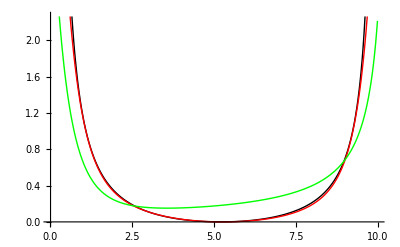

```mathematica
Plot[{Veff[q]-0.41785627512329665,Vneural[q],2.2702215827492807/(1-2.28193363198688031844134936177499234771`15.579481563849557 (-10+q))+(0.5 (7.84981043847567867526466846778120799959`16.902975241431633-1.98478505654595582600971794407924241581`13.968427608229574 q))/(1+1.96463934587803862042779336402037631125`15.488000161719805 q+1.65546339874091400723053205248310776806`15.488000161719805 q^2+0.65914546179897474080470342579414862122`15.488000161719805 q^3)},{q,0.01,9.99},PlotStyle->{{Black,Thin},{Red,Thin},{Green,Thick}}]
```

```mathematica
0.5*Evaluate[PadeApproximant[Vneural[q],{q,0,{1,3}}]] + 0.5*Evaluate[PadeApproximant[Vneural[q],{q,10,{0,1}}]]
```

2.27022/(1-2.28193363198688 (-10+q))+(0.5 (7.849810438475679-1.984785056546 q))/(1+1.96463934587804 q+1.65546339874091 q^2+0.659145461798975 q^3)

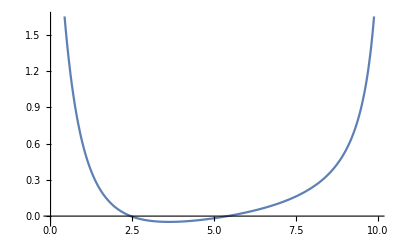

```mathematica
Plot[2.2702215827492807/(1-2.28193363198688031844134936177499234771`15.579481563849557 (-10+r))+(0.5 (7.84981043847567867526466846778120799959`16.902975241431633-4.31954711277390271178588765178643331225`14.925482167630033 r))/(1+1.66721024557974856312576034845132008277`16.07528999459858 r+0.99591903481512092374763281516565993397`16.07528999459858 r^2),{r,0.01,9.99}]
```

```mathematica
FullSimplify[%]
```

(1.01212070898-0.625613920602 r)/(-1257.18566249+r (348.708391822+r (-32.3105321314+1. r)))

```mathematica
FullSimplify[Vneural[r]]
```

-0.17821185535293862+(0.97554458648491753749 (1+(1.364016337198722072 (1+2.65624621563005495 ⅇ^(-1.18099892139434815 r))^0.487025350332260132 (1+2.279975208353120797 ⅇ^(-0.909640252590179443 r))^0.491697192192077637 (1+0.5492840853881936296 ⅇ^(-0.85328972339630127 r))^0.327043652534484863 (1+2.167527608903181276 ⅇ^(-0.805604994297027588 r))^0.656582534313201904 (1+1.184002383335151101 ⅇ^(-0.606638908386230469 r))^0.828496038913726807 (1+17.1209269525394856 ⅇ^(-0.0374943502247333527 r))^0.0771363154053688049 (1+2.257419475296943759 ⅇ^(0.0139716370031237602 r))^0.0463119819760322571 (1+1.115853289108205991 ⅇ^(0.39266243577003479 r))^0.0789011567831039429)/((1+2.283844080535936374 ⅇ^(0.315275341272354126 r))^0.275593042373657227 (1+0.5735441496949904287 ⅇ^(0.479208052158355713 r))^0.218226447701454163 (1+0.5446617183377491547 ⅇ^(0.506511926651000977 r))^0.451765865087509155 (1+4.0084785699321575 ⅇ^(0.550239264965057373 r))^0.0813458263874053955 (1+1.123362937188797835 ⅇ^(0.734994351863861084 r))^0.592603802680969238 (1+0.314271617085676808 ⅇ^(0.841557145118713379 r))^0.363228559494018555 (1+0.353611725633524173 ⅇ^(1.01462221145629883 r))^0.107204638421535492 (1+0.288225878447567903 ⅇ^(1.04568994045257568 r))^0.777192950248718262))^0.3358784019947052 (1+(0.94178145575339555873 (1+1.184002383335151101 ⅇ^(-0.606638908386230469 r))^0.257632404565811157 (1+0.5735441496949904287 ⅇ^(0.479208052158355713 r))^0.0532430857419967651 (1+1.123362937188797835 ⅇ^(0.734994351863861084 r))^0.208737120032310486)/((1+2.65624621563005495 ⅇ^(-1.18099892139434815 r))^0.365412592887878418 (1+2.279975208353120797 ⅇ^(-0.909640252590179443 r))^0.425033777952194214 (1+0.5492840853881936296 ⅇ^(-0.85328972339630127 r))^0.493751555681228638 (1+2.167527608903181276 ⅇ^(-0.805604994297027588 r))^0.395271062850952148 (1+17.1209269525394856 ⅇ^(-0.0374943502247333527 r))^0.549092769622802734 (1+2.257419475296943759 ⅇ^(0.0139716370031237602 r))^0.375790655612945557 (1+2.283844080535936374 ⅇ^(0.315275341272354126 r))^0.00169695878867059946 (1+1.115853289108205991 ⅇ^(0.39266243577003479 r))^0.283151745796203613 (1+0.5446617183377491547 ⅇ^(0.506511926651000977 r))^0.458329468965530396 (1+4.0084785699321575 ⅇ^(0.550239264965057373 r))^0.500186741352081299 (1+0.314271617085676808 ⅇ^(0.841557145118713379 r))^0.476442694664001465 (1+0.353611725633524173 ⅇ^(1.01462221145629883 r))^0.452598363161087036 (1+0.288225878447567903 ⅇ^(1.04568994045257568 r))^0.580199658870697022))^0.425437331199645996 (1+(1.722436494979243919 (1+2.65624621563005495 ⅇ^(-1.18099892139434815 r))^0.832920432090759277 (1+2.279975208353120797 ⅇ^(-0.909640252590179443 r))^0.270253658294677734 (1+0.5492840853881936296 ⅇ^(-0.85328972339630127 r))^0.241045206785202026 (1+1.184002383335151101 ⅇ^(-0.606638908386230469 r))^0.0196024421602487564 (1+17.1209269525394856 ⅇ^(-0.0374943502247333527 r))^0.747711420059204102 (1+2.257419475296943759 ⅇ^(0.0139716370031237602 r))^0.546054601669311523 (1+2.283844080535936374 ⅇ^(0.315275341272354126 r))^0.376511633396148682 (1+4.0084785699321575 ⅇ^(0.550239264965057373 r))^0.203900769352912903 (1+1.123362937188797835 ⅇ^(0.734994351863861084 r))^0.34064522385597229)/((1+2.167527608903181276 ⅇ^(-0.805604994297027588 r))^0.0334256663918495178 (1+1.115853289108205991 ⅇ^(0.39266243577003479 r))^0.12863081693649292 (1+0.5735441496949904287 ⅇ^(0.479208052158355713 r))^0.391392290592193604 (1+0.5446617183377491547 ⅇ^(0.506511926651000977 r))^0.517592430114746094 (1+0.314271617085676808 ⅇ^(0.841557145118713379 r))^0.5025901198387146 (1+0.353611725633524173 ⅇ^(1.01462221145629883 r))^0.357558012008666992 (1+0.288225878447567903 ⅇ^(1.04568994045257568 r))^0.491373509168624878))^0.239546641707420349 (1+(1.48967919619324211 (1+2.65624621563005495 ⅇ^(-1.18099892139434815 r))^1.05484461784362793 (1+2.279975208353120797 ⅇ^(-0.909640252590179443 r))^0.757246494293212891 (1+0.5492840853881936296 ⅇ^(-0.85328972339630127 r))^0.808953523635864258 (1+2.167527608903181276 ⅇ^(-0.805604994297027588 r))^0.157287389039993286 (1+1.184002383335151101 ⅇ^(-0.606638908386230469 r))^0.785429954528808594 (1+17.1209269525394856 ⅇ^(-0.0374943502247333527 r))^0.269974738359451294 (1+4.0084785699321575 ⅇ^(0.550239264965057373 r))^0.0286881942301988602)/((1+2.257419475296943759 ⅇ^(0.0139716370031237602 r))^0.232629165053367615 (1+2.283844080535936374 ⅇ^(0.315275341272354126 r))^0.13664989173412323 (1+1.115853289108205991 ⅇ^(0.39266243577003479 r))^0.295940130949020386 (1+0.5735441496949904287 ⅇ^(0.479208052158355713 r))^0.0278897508978843689 (1+0.5446617183377491547 ⅇ^(0.506511926651000977 r))^0.0616010092198848724 (1+1.123362937188797835 ⅇ^(0.734994351863861084 r))^0.485578000545501709 (1+0.314271617085676808 ⅇ^(0.841557145118713379 r))^0.325897514820098877 (1+0.353611725633524173 ⅇ^(1.01462221145629883 r))^0.453324258327484131 (1+0.288225878447567903 ⅇ^(1.04568994045257568 r))^0.469195067882537842))^0.157241001725196838 (1+(0.98842130664209519382 (1+2.65624621563005495 ⅇ^(-1.18099892139434815 r))^0.0271993055939674377 (1+2.279975208353120797 ⅇ^(-0.909640252590179443 r))^0.062702566385269165 (1+2.257419475296943759 ⅇ^(0.0139716370031237602 r))^0.0186885949224233627)/((1+0.5492840853881936296 ⅇ^(-0.85328972339630127 r))^0.533879637718200684 (1+2.167527608903181276 ⅇ^(-0.805604994297027588 r))^0.421765923500061035 (1+1.184002383335151101 ⅇ^(-0.606638908386230469 r))^0.683597803115844727 (1+17.1209269525394856 ⅇ^(-0.0374943502247333527 r))^0.239125028252601624 (1+2.283844080535936374 ⅇ^(0.315275341272354126 r))^0.287952214479446411 (1+1.115853289108205991 ⅇ^(0.39266243577003479 r))^0.385447651147842407 (1+0.5735441496949904287 ⅇ^(0.479208052158355713 r))^0.297832190990447998 (1+0.5446617183377491547 ⅇ^(0.506511926651000977 r))^0.104869544506072998 (1+4.0084785699321575 ⅇ^(0.550239264965057373 r))^0.467367023229598999 (1+1.123362937188797835 ⅇ^(0.734994351863861084 r))^0.303333282470703125 (1+0.314271617085676808 ⅇ^(0.841557145118713379 r))^0.700680851936340332 (1+0.353611725633524173 ⅇ^(1.01462221145629883 r))^0.382147401571273804 (1+0.288225878447567903 ⅇ^(1.04568994045257568 r))^0.0285618174821138382))^0.217771634459495544 (1+(0.9992043906394965793622 (1+2.167527608903181276 ⅇ^(-0.805604994297027588 r))^0.206848233938217163 (1+1.184002383335151101 ⅇ^(-0.606638908386230469 r))^0.371633440256118774 (1+17.1209269525394856 ⅇ^(-0.0374943502247333527 r))^0.0214559398591518402 (1+2.257419475296943759 ⅇ^(0.0139716370031237602 r))^0.0677744150161743164 (1+2.283844080535936374 ⅇ^(0.315275341272354126 r))^0.425244063138961792 (1+1.115853289108205991 ⅇ^(0.39266243577003479 r))^0.0832597687840461731 (1+0.5735441496949904287 ⅇ^(0.479208052158355713 r))^0.192885026335716248 (1+0.5446617183377491547 ⅇ^(0.506511926651000977 r))^0.26603156328201294 (1+0.314271617085676808 ⅇ^(0.841557145118713379 r))^0.325713753700256348 (1+0.353611725633524173 ⅇ^(1.01462221145629883 r))^0.213795542716979981)/((1+2.65624621563005495 ⅇ^(-1.18099892139434815 r))^0.27548786997795105 (1+2.279975208353120797 ⅇ^(-0.909640252590179443 r))^0.0813861340284347534 (1+0.5492840853881936296 ⅇ^(-0.85328972339630127 r))^0.00817891769111156464 (1+4.0084785699321575 ⅇ^(0.550239264965057373 r))^0.208190113306045532 (1+1.123362937188797835 ⅇ^(0.734994351863861084 r))^0.409300535917282105 (1+0.288225878447567903 ⅇ^(1.04568994045257568 r))^0.00772963976487517357))^0.0318136997520923615 (1+(0.995972287216391244213 (1+2.65624621563005495 ⅇ^(-1.18099892139434815 r))^0.128003939986228943 (1+2.167527608903181276 ⅇ^(-0.805604994297027588 r))^0.315165311098098755 (1+2.283844080535936374 ⅇ^(0.315275341272354126 r))^0.306221157312393189 (1+0.5735441496949904287 ⅇ^(0.479208052158355713 r))^0.0347600542008876801 (1+4.0084785699321575 ⅇ^(0.550239264965057373 r))^0.176786422729492188 (1+0.314271617085676808 ⅇ^(0.841557145118713379 r))^0.0643285512924194336 (1+0.353611725633524173 ⅇ^(1.01462221145629883 r))^0.0252413488924503326 (1+0.288225878447567903 ⅇ^(1.04568994045257568 r))^0.0578265413641929627)/((1+2.279975208353120797 ⅇ^(-0.909640252590179443 r))^0.0229592379182577133 (1+0.5492840853881936296 ⅇ^(-0.85328972339630127 r))^0.46583893895149231 (1+1.184002383335151101 ⅇ^(-0.606638908386230469 r))^0.395021706819534302 (1+17.1209269525394856 ⅇ^(-0.0374943502247333527 r))^0.0850283876061439514 (1+2.257419475296943759 ⅇ^(0.0139716370031237602 r))^0.401004999876022339 (1+1.115853289108205991 ⅇ^(0.39266243577003479 r))^0.00118251063395291567 (1+0.5446617183377491547 ⅇ^(0.506511926651000977 r))^0.085003197193145752 (1+1.123362937188797835 ⅇ^(0.734994351863861084 r))^0.0894400179386138916))^0.200297683477401733 (1+(1.0606876949137755344 (1+2.65624621563005495 ⅇ^(-1.18099892139434815 r))^0.483188062906265259 (1+2.279975208353120797 ⅇ^(-0.909640252590179443 r))^0.312789112329483032 (1+2.167527608903181276 ⅇ^(-0.805604994297027588 r))^0.394656062126159668 (1+1.184002383335151101 ⅇ^(-0.606638908386230469 r))^0.0205911900848150253 (1+17.1209269525394856 ⅇ^(-0.0374943502247333527 r))^0.115866787731647492 (1+0.5446617183377491547 ⅇ^(0.506511926651000977 r))^0.184025421738624573 (1+1.123362937188797835 ⅇ^(0.734994351863861084 r))^0.06525382399559021 (1+0.314271617085676808 ⅇ^(0.841557145118713379 r))^0.113183014094829559 (1+0.288225878447567903 ⅇ^(1.04568994045257568 r))^0.209348008036613464)/((1+0.5492840853881936296 ⅇ^(-0.85328972339630127 r))^0.468787401914596558 (1+2.257419475296943759 ⅇ^(0.0139716370031237602 r))^0.0392057299613952637 (1+2.283844080535936374 ⅇ^(0.315275341272354126 r))^0.364840716123580933 (1+1.115853289108205991 ⅇ^(0.39266243577003479 r))^0.243732273578643799 (1+0.5735441496949904287 ⅇ^(0.479208052158355713 r))^0.0955588966608047485 (1+4.0084785699321575 ⅇ^(0.550239264965057373 r))^0.177694261074066162 (1+0.353611725633524173 ⅇ^(1.01462221145629883 r))^0.44926723837852478))^0.78313899040222168 (1+(0.835289236346092671 (1+2.65624621563005495 ⅇ^(-1.18099892139434815 r))^0.590564370155334473 (1+2.279975208353120797 ⅇ^(-0.909640252590179443 r))^0.0949602574110031128 (1+0.5492840853881936296 ⅇ^(-0.85328972339630127 r))^0.359727382659912109 (1+2.167527608903181276 ⅇ^(-0.805604994297027588 r))^0.745526015758514404 (1+1.184002383335151101 ⅇ^(-0.606638908386230469 r))^0.813979029655456543 (1+2.257419475296943759 ⅇ^(0.0139716370031237602 r))^0.402234971523284912 (1+2.283844080535936374 ⅇ^(0.315275341272354126 r))^0.331292212009429932 (1+1.115853289108205991 ⅇ^(0.39266243577003479 r))^0.291121989488601685 (1+0.5735441496949904287 ⅇ^(0.479208052158355713 r))^0.0960875228047370911 (1+0.5446617183377491547 ⅇ^(0.506511926651000977 r))^0.423024207353591919 (1+0.314271617085676808 ⅇ^(0.841557145118713379 r))^0.248223364353179932 (1+0.288225878447567903 ⅇ^(1.04568994045257568 r))^0.287584573030471802)/((1+17.1209269525394856 ⅇ^(-0.0374943502247333527 r))^0.020056258887052536 (1+4.0084785699321575 ⅇ^(0.550239264965057373 r))^0.198851853609085083 (1+1.123362937188797835 ⅇ^(0.734994351863861084 r))^0.247116073966026306 (1+0.353611725633524173 ⅇ^(1.01462221145629883 r))^0.218460723757743835))^0.0785701274871826172 (1+(0.997433276852436103621 (1+2.65624621563005495 ⅇ^(-1.18099892139434815 r))^0.0779188647866249085 (1+2.167527608903181276 ⅇ^(-0.805604994297027588 r))^0.159989655017852783 (1+1.184002383335151101 ⅇ^(-0.606638908386230469 r))^0.198004454374313355 (1+2.257419475296943759 ⅇ^(0.0139716370031237602 r))^0.336139440536499023 (1+2.283844080535936374 ⅇ^(0.315275341272354126 r))^0.207298919558525085 (1+0.5735441496949904287 ⅇ^(0.479208052158355713 r))^0.326507121324539185 (1+4.0084785699321575 ⅇ^(0.550239264965057373 r))^0.406404554843902588 (1+1.123362937188797835 ⅇ^(0.734994351863861084 r))^0.193704366683959961 (1+0.314271617085676808 ⅇ^(0.841557145118713379 r))^0.166757136583328247 (1+0.353611725633524173 ⅇ^(1.01462221145629883 r))^0.0779000967741012573 (1+0.288225878447567903 ⅇ^(1.04568994045257568 r))^0.298744499683380127)/((1+2.279975208353120797 ⅇ^(-0.909640252590179443 r))^0.345067739486694336 (1+0.5492840853881936296 ⅇ^(-0.85328972339630127 r))^0.325941324234008789 (1+17.1209269525394856 ⅇ^(-0.0374943502247333527 r))^0.0483442805707454681 (1+1.115853289108205991 ⅇ^(0.39266243577003479 r))^0.355095058679580689 (1+0.5446617183377491547 ⅇ^(0.506511926651000977 r))^0.283738136291503906))^0.0359038971364498138 (1+(0.8305069112948813935 (1+2.65624621563005495 ⅇ^(-1.18099892139434815 r))^0.00155679183080792427 (1+2.279975208353120797 ⅇ^(-0.909640252590179443 r))^0.431801855564117432 (1+2.167527608903181276 ⅇ^(-0.805604994297027588 r))^0.311424523591995239 (1+1.184002383335151101 ⅇ^(-0.606638908386230469 r))^0.0159458201378583908 (1+0.5446617183377491547 ⅇ^(0.506511926651000977 r))^0.0897991955280303955 (1+0.353611725633524173 ⅇ^(1.01462221145629883 r))^0.575914442539215088 (1+0.288225878447567903 ⅇ^(1.04568994045257568 r))^0.598388910293579102)/((1+0.5492840853881936296 ⅇ^(-0.85328972339630127 r))^0.511632144451141357 (1+17.1209269525394856 ⅇ^(-0.0374943502247333527 r))^1.05720245838165283 (1+2.257419475296943759 ⅇ^(0.0139716370031237602 r))^0.115369997918605804 (1+2.283844080535936374 ⅇ^(0.315275341272354126 r))^0.608417630195617676 (1+1.115853289108205991 ⅇ^(0.39266243577003479 r))^0.306806832551956177 (1+0.5735441496949904287 ⅇ^(0.479208052158355713 r))^0.120103113353252411 (1+4.0084785699321575 ⅇ^(0.550239264965057373 r))^0.147196829319000244 (1+1.123362937188797835 ⅇ^(0.734994351863861084 r))^0.00275461352430284023 (1+0.314271617085676808 ⅇ^(0.841557145118713379 r))^0.112560391426086426))^0.977552890777587891 (1+(0.7776142837294105484 (1+2.167527608903181276 ⅇ^(-0.805604994297027588 r))^0.201121360063552856 (1+1.184002383335151101 ⅇ^(-0.606638908386230469 r))^0.0000892246680450625718 (1+1.123362937188797835 ⅇ^(0.734994351863861084 r))^0.195696517825126648 (1+0.314271617085676808 ⅇ^(0.841557145118713379 r))^0.0715732872486114502 (1+0.353611725633524173 ⅇ^(1.01462221145629883 r))^0.236384361982345581 (1+0.288225878447567903 ⅇ^(1.04568994045257568 r))^0.616934061050415039)/((1+2.65624621563005495 ⅇ^(-1.18099892139434815 r))^0.182935938239097595 (1+2.279975208353120797 ⅇ^(-0.909640252590179443 r))^0.407113611698150635 (1+0.5492840853881936296 ⅇ^(-0.85328972339630127 r))^0.438442498445510864 (1+17.1209269525394856 ⅇ^(-0.0374943502247333527 r))^0.933978378772735596 (1+2.257419475296943759 ⅇ^(0.0139716370031237602 r))^0.330480098724365234 (1+2.283844080535936374 ⅇ^(0.315275341272354126 r))^0.171680927276611328 (1+1.115853289108205991 ⅇ^(0.39266243577003479 r))^0.413535028696060181 (1+0.5735441496949904287 ⅇ^(0.479208052158355713 r))^0.269152820110321045 (1+0.5446617183377491547 ⅇ^(0.506511926651000977 r))^0.0119976280257105827 (1+4.0084785699321575 ⅇ^(0.550239264965057373 r))^0.515566587448120117))^0.725786805152893066 (1+(0.283497478882894932 (1+2.279975208353120797 ⅇ^(-0.909640252590179443 r))^0.696307659149169922 (1+2.167527608903181276 ⅇ^(-0.805604994297027588 r))^0.62399977445602417 (1+1.184002383335151101 ⅇ^(-0.606638908386230469 r))^0.0225856583565473557 (1+0.5735441496949904287 ⅇ^(0.479208052158355713 r))^0.657242119312286377 (1+0.5446617183377491547 ⅇ^(0.506511926651000977 r))^0.502126514911651611 (1+0.314271617085676808 ⅇ^(0.841557145118713379 r))^1.10190558433532715 (1+0.353611725633524173 ⅇ^(1.01462221145629883 r))^1.02972960472106934 (1+0.288225878447567903 ⅇ^(1.04568994045257568 r))^1.0209805965423584)/((1+2.65624621563005495 ⅇ^(-1.18099892139434815 r))^0.0485259890556335449 (1+0.5492840853881936296 ⅇ^(-0.85328972339630127 r))^0.302250742912292481 (1+17.1209269525394856 ⅇ^(-0.0374943502247333527 r))^2.84723377227783203 (1+2.257419475296943759 ⅇ^(0.0139716370031237602 r))^0.832841217517852783 (1+2.283844080535936374 ⅇ^(0.315275341272354126 r))^1.21964418888092041 (1+1.115853289108205991 ⅇ^(0.39266243577003479 r))^0.0507678873836994171 (1+4.0084785699321575 ⅇ^(0.550239264965057373 r))^2.1570131778717041 (1+1.123362937188797835 ⅇ^(0.734994351863861084 r))^0.162784382700920105))^0.977145195007324219)/((1+(1.707009503212048044 (1+2.65624621563005495 ⅇ^(-1.18099892139434815 r))^0.550718188285827637 (1+0.5492840853881936296 ⅇ^(-0.85328972339630127 r))^0.446283340454101563 (1+2.167527608903181276 ⅇ^(-0.805604994297027588 r))^0.191862314939498901 (1+1.184002383335151101 ⅇ^(-0.606638908386230469 r))^0.19669601321220398 (1+17.1209269525394856 ⅇ^(-0.0374943502247333527 r))^0.648149728775024414 (1+2.257419475296943759 ⅇ^(0.0139716370031237602 r))^0.446319490671157837 (1+1.115853289108205991 ⅇ^(0.39266243577003479 r))^0.223724812269210815 (1+0.5735441496949904287 ⅇ^(0.479208052158355713 r))^0.268568098545074463 (1+4.0084785699321575 ⅇ^(0.550239264965057373 r))^0.0143752256408333778 (1+1.123362937188797835 ⅇ^(0.734994351863861084 r))^0.105345122516155243 (1+0.353611725633524173 ⅇ^(1.01462221145629883 r))^0.120661094784736633)/((1+2.279975208353120797 ⅇ^(-0.909640252590179443 r))^0.126682236790657044 (1+2.283844080535936374 ⅇ^(0.315275341272354126 r))^0.0372897274792194367 (1+0.5446617183377491547 ⅇ^(0.506511926651000977 r))^0.34490436315536499 (1+0.314271617085676808 ⅇ^(0.841557145118713379 r))^0.0210580211132764816 (1+0.288225878447567903 ⅇ^(1.04568994045257568 r))^0.532898008823394775))^0.0383459404110908508 (1+(1.017044369853383103 (1+0.5492840853881936296 ⅇ^(-0.85328972339630127 r))^0.356861919164657593 (1+17.1209269525394856 ⅇ^(-0.0374943502247333527 r))^0.362605035305023193 (1+2.257419475296943759 ⅇ^(0.0139716370031237602 r))^0.444015085697174072 (1+2.283844080535936374 ⅇ^(0.315275341272354126 r))^0.410037696361541748 (1+1.115853289108205991 ⅇ^(0.39266243577003479 r))^0.20612335205078125 (1+0.5735441496949904287 ⅇ^(0.479208052158355713 r))^0.124602377414703369 (1+4.0084785699321575 ⅇ^(0.550239264965057373 r))^0.348867565393447876 (1+0.353611725633524173 ⅇ^(1.01462221145629883 r))^0.0764559656381607056 (1+0.288225878447567903 ⅇ^(1.04568994045257568 r))^0.0108485091477632523)/((1+2.65624621563005495 ⅇ^(-1.18099892139434815 r))^0.461559116840362549 (1+2.279975208353120797 ⅇ^(-0.909640252590179443 r))^0.156572744250297546 (1+2.167527608903181276 ⅇ^(-0.805604994297027588 r))^0.109845392405986786 (1+1.184002383335151101 ⅇ^(-0.606638908386230469 r))^0.056941792368888855 (1+0.5446617183377491547 ⅇ^(0.506511926651000977 r))^0.179874956607818604 (1+1.123362937188797835 ⅇ^(0.734994351863861084 r))^0.0167200081050395966 (1+0.314271617085676808 ⅇ^(0.841557145118713379 r))^0.136125192046165466))^0.593192875385284424 (1+(1.513538275881397729 (1+2.65624621563005495 ⅇ^(-1.18099892139434815 r))^0.191638931632041931 (1+2.279975208353120797 ⅇ^(-0.909640252590179443 r))^0.164189130067825317 (1+0.5492840853881936296 ⅇ^(-0.85328972339630127 r))^0.314205437898635864 (1+2.167527608903181276 ⅇ^(-0.805604994297027588 r))^0.284185796976089478 (1+1.184002383335151101 ⅇ^(-0.606638908386230469 r))^0.492393314838409424 (1+17.1209269525394856 ⅇ^(-0.0374943502247333527 r))^0.730597257614135742 (1+2.283844080535936374 ⅇ^(0.315275341272354126 r))^0.34447053074836731 (1+1.115853289108205991 ⅇ^(0.39266243577003479 r))^0.3263968825340271 (1+0.5446617183377491547 ⅇ^(0.506511926651000977 r))^0.32239222526550293 (1+4.0084785699321575 ⅇ^(0.550239264965057373 r))^0.463819056749343872 (1+0.288225878447567903 ⅇ^(1.04568994045257568 r))^0.112276405096054077)/((1+2.257419475296943759 ⅇ^(0.0139716370031237602 r))^0.27664715051651001 (1+0.5735441496949904287 ⅇ^(0.479208052158355713 r))^0.325027525424957275 (1+1.123362937188797835 ⅇ^(0.734994351863861084 r))^0.155903086066246033 (1+0.314271617085676808 ⅇ^(0.841557145118713379 r))^0.400900393724441528 (1+0.353611725633524173 ⅇ^(1.01462221145629883 r))^0.425435423851013184))^0.0595180578529834747)